# θ Derivatives

```mathematica
dθC1 = FullSimplify[ComplexExpand[Conjugate[C1], α] * D[C1, θ]]
```

-1/(729 Δ^4)2 p κ (-3 ⅈ Im[α] (3 Δ Cos[θ]+4 p κ Cos[2 θ] Re[α])+√3 Re[α] (3 Δ+8 p κ Cos[θ] Re[α]) Sin[θ]) (-9 √3 Δ^2+p κ (3 √3 p κ Im[α]^2+√3 Re[α] (6 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])-6 ⅈ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))

```mathematica
dθC3 = FullSimplify[ComplexExpand[Conjugate[C3], α] * D[C3, θ]]
```

1/(729 Δ^4)p κ (9 √3 Δ^2-√3 p^2 κ^2 (3 Im[α]^2+Re[α]^2+Cos[2 θ] (Conjugate[α]^2-α (α+2 Re[α])))-3 p α Δ κ (√3 Cos[θ]+3 Sin[θ])+6 p κ Conjugate[α] Cos[θ] (√3 Δ+2 p κ Re[α] Sin[θ])) (-9 Δ Conjugate[α] Cos[θ]+12 p α κ Cos[2 θ] Re[α]+3 √3 Δ (-2 α+Conjugate[α]) Sin[θ]+4 √3 p κ (α-2 Conjugate[α]) Re[α] Sin[2 θ])

```mathematica
dθC5 = FullSimplify[ComplexExpand[Conjugate[C5], α] * D[C5, θ]]
```

1/(729 Δ^4)p κ (9 α Δ Cos[θ]-12 p κ Conjugate[α] Cos[2 θ] Re[α]+3 √3 Δ (α-2 Conjugate[α]) Sin[θ]+2 √3 p κ (Conjugate[α]^2-α (α+2 Re[α])) Sin[2 θ]) (9 √3 Δ (Δ+p α κ Cos[θ])+p κ (-6 √3 Δ Cos[θ] Re[α]+9 Δ Conjugate[α] Sin[θ]+p κ (2 √3 Cos[2 θ] Re[α] (-3 α+4 Re[α])-√3 (3 Im[α]^2+Re[α]^2)-6 α Re[α] Sin[2 θ])))

```mathematica
dθχ1 = Simplify[ComplexExpand[Conjugate[C1], α] * C1 * ComplexExpand[Conjugate[χ1]]. D[χ1, θ]]
```

(p (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)-6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)+6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (n Cos[θ] (ⅈ (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Sin[θ])+4 p (2 ⅈ n w^2 κ (-2+w+2 κ)+(-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ])))/(729 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)

```mathematica
dθχ3 = Simplify[ComplexExpand[Conjugate[C3], α] * C3 * ComplexExpand[Conjugate[χ3]]. D[χ3, θ]]
```

(p (-3 √3 p^2 κ^2 Im[α]^2+√3 p^2 κ^2 (-1+8 Cos[2 θ]) Re[α]^2+9 Δ (√3 (Δ+p α κ Cos[θ])-p κ Conjugate[α] Sin[θ])-6 p κ Re[α] (√3 Δ Cos[θ]+p α κ (√3 Cos[2 θ]-Sin[2 θ]))) (-64 ⅈ n p w^2 κ+32 ⅈ n p w^3 κ+64 ⅈ n p w^2 κ^2-2 ⅈ n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+√3 n^2 p (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[2 θ]-32 p w^2 κ^2 Cos[π/6+2 θ]+32 ⅈ √3 n Sin[θ]-64 ⅈ √3 n w Sin[θ]+80 ⅈ √3 n w^2 Sin[θ]-48 ⅈ √3 n w^3 Sin[θ]+10 ⅈ √3 n w^4 Sin[θ]-128 ⅈ √3 n κ Sin[θ]+192 ⅈ √3 n w κ Sin[θ]-160 ⅈ √3 n w^2 κ Sin[θ]+48 ⅈ √3 n w^3 κ Sin[θ]+192 ⅈ √3 n κ^2 Sin[θ]-192 ⅈ √3 n w κ^2 Sin[θ]+80 ⅈ √3 n w^2 κ^2 Sin[θ]-128 ⅈ √3 n κ^3 Sin[θ]+64 ⅈ √3 n w κ^3 Sin[θ]+32 ⅈ √3 n κ^4 Sin[θ]-16 n^2 p Sin[2 θ]+32 n^2 p w Sin[2 θ]-40 n^2 p w^2 Sin[2 θ]+24 n^2 p w^3 Sin[2 θ]-5 n^2 p w^4 Sin[2 θ]+64 n^2 p κ Sin[2 θ]-96 n^2 p w κ Sin[2 θ]+80 n^2 p w^2 κ Sin[2 θ]-24 n^2 p w^3 κ Sin[2 θ]-96 n^2 p κ^2 Sin[2 θ]+96 n^2 p w κ^2 Sin[2 θ]-40 n^2 p w^2 κ^2 Sin[2 θ]+64 n^2 p κ^3 Sin[2 θ]-32 n^2 p w κ^3 Sin[2 θ]-16 n^2 p κ^4 Sin[2 θ]) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]-3 Sin[θ])+3 ⅈ p κ Im[α] (-3 Δ (√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]-Sin[2 θ]))+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]+6 Sin[2 θ])))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)

```mathematica
dθχ5 = Simplify[ComplexExpand[Conjugate[C5], α] * C5 * ComplexExpand[Conjugate[χ5]]. D[χ5, θ]]
```

(p (9 √3 Δ^2-3 √3 p α Δ κ Cos[θ]+√3 p^2 α^2 κ^2 Cos[2 θ]-√3 p^2 κ^2 Conjugate[α]^2 Cos[2 θ]-3 √3 p^2 κ^2 Im[α]^2+2 √3 p^2 α κ^2 Cos[2 θ] Re[α]-√3 p^2 κ^2 Re[α]^2+9 p α Δ κ Sin[θ]+6 p κ Conjugate[α] Cos[θ] (√3 Δ-2 p κ Re[α] Sin[θ])) (32 n p w^2 κ (-2+w+2 κ)-2 n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+ⅈ √3 p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]+2 n (-√3 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+ⅈ n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Cos[θ]) Sin[θ]+8 ⅈ p (-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ]) (-3 ⅈ √3 p^2 κ^2 Im[α]^2+ⅈ (9 √3 Δ^2+3 p Δ κ Re[α] (√3 Cos[θ]+3 Sin[θ])+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]-6 Sin[2 θ]))+3 p κ Im[α] (3 Δ (-√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]+Sin[2 θ]))))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)

# p Derivatives

```mathematica
dpC1 = FullSimplify[ComplexExpand[Conjugate[C1], α] * D[C1, p]]
```

1/(729 Δ^4)2 κ (3 √3 p κ Im[α]^2+√3 Re[α] (3 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])+3 ⅈ Im[α] (3 Δ+8 p κ Cos[θ] Re[α]) Sin[θ]) (-9 √3 Δ^2+p κ (3 √3 p κ Im[α]^2+√3 Re[α] (6 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])-6 ⅈ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))

```mathematica
dpC3 = FullSimplify[ComplexExpand[Conjugate[C3], α] * D[C3, p]]
```

1/(729 Δ^4)κ (3 √3 Δ (-2 α+Conjugate[α]) Cos[θ]+4 √3 p κ (α-2 Conjugate[α]) Cos[2 θ] Re[α]+2 √3 p κ (3 Im[α]^2+Re[α]^2)+9 Δ Conjugate[α] Sin[θ]-12 p α κ Re[α] Sin[2 θ]) (3 √3 Δ (-3 Δ+p α κ Cos[θ])+p κ (-6 √3 Δ Conjugate[α] Cos[θ]+√3 p κ (3 Im[α]^2+Re[α]^2)+√3 p κ Cos[2 θ] (Conjugate[α]^2-α (α+2 Re[α]))+9 α Δ Sin[θ]-6 p κ Conjugate[α] Re[α] Sin[2 θ]))

```mathematica
dpC5 = FullSimplify[ComplexExpand[Conjugate[C5], α] * D[C5, p]]
```

-1/(729 Δ^4)κ (-3 √3 Δ (α-2 Conjugate[α]) Cos[θ]-2 √3 p κ (3 Im[α]^2+Re[α]^2)+2 √3 p κ Cos[2 θ] (-Conjugate[α]^2+α (α+2 Re[α]))+9 α Δ Sin[θ]-12 p κ Conjugate[α] Re[α] Sin[2 θ]) (-9 √3 Δ^2+3 p Δ κ (√3 (-2 α+Conjugate[α]) Cos[θ]-3 Conjugate[α] Sin[θ])+p^2 κ^2 (2 √3 (α-2 Conjugate[α]) Cos[2 θ] Re[α]+√3 (3 Im[α]^2+Re[α]^2)+6 α Re[α] Sin[2 θ]))

```mathematica
dpχ1 = Simplify[ComplexExpand[Conjugate[C1], α] * C1 * ComplexExpand[Conjugate[χ1]]. D[χ1, p]]
```

-(((-p (16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2)+p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]-2 ⅈ n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)-6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)+6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))/(1458 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2))

```mathematica
dpχ3 = Simplify[ComplexExpand[Conjugate[C3], α] * C3 * ComplexExpand[Conjugate[χ3]]. D[χ3, p]]
```

((-3 √3 p^2 κ^2 Im[α]^2+√3 p^2 κ^2 (-1+8 Cos[2 θ]) Re[α]^2+9 Δ (√3 (Δ+p α κ Cos[θ])-p κ Conjugate[α] Sin[θ])-6 p κ Re[α] (√3 Δ Cos[θ]+p α κ (√3 Cos[2 θ]-Sin[2 θ]))) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]-3 Sin[θ])+3 ⅈ p κ Im[α] (-3 Δ (√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]-Sin[2 θ]))+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]+6 Sin[2 θ])) (32 n^2 p-64 n^2 p w+80 n^2 p w^2-48 n^2 p w^3+10 n^2 p w^4-128 n^2 p κ+192 n^2 p w κ-160 n^2 p w^2 κ+48 n^2 p w^3 κ+192 n^2 p κ^2-192 n^2 p w κ^2+32 p w^2 κ^2+80 n^2 p w^2 κ^2-128 n^2 p κ^3+64 n^2 p w κ^3+32 n^2 p κ^4-2 ⅈ √3 n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+n^2 p (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[2 θ]-32 ⅈ n Sin[θ]+64 ⅈ n w Sin[θ]-80 ⅈ n w^2 Sin[θ]+48 ⅈ n w^3 Sin[θ]-10 ⅈ n w^4 Sin[θ]+128 ⅈ n κ Sin[θ]-192 ⅈ n w κ Sin[θ]+160 ⅈ n w^2 κ Sin[θ]-48 ⅈ n w^3 κ Sin[θ]-192 ⅈ n κ^2 Sin[θ]+192 ⅈ n w κ^2 Sin[θ]-80 ⅈ n w^2 κ^2 Sin[θ]+128 ⅈ n κ^3 Sin[θ]-64 ⅈ n w κ^3 Sin[θ]-32 ⅈ n κ^4 Sin[θ]+16 √3 n^2 p Sin[2 θ]-32 √3 n^2 p w Sin[2 θ]+40 √3 n^2 p w^2 Sin[2 θ]-24 √3 n^2 p w^3 Sin[2 θ]+5 √3 n^2 p w^4 Sin[2 θ]-64 √3 n^2 p κ Sin[2 θ]+96 √3 n^2 p w κ Sin[2 θ]-80 √3 n^2 p w^2 κ Sin[2 θ]+24 √3 n^2 p w^3 κ Sin[2 θ]+96 √3 n^2 p κ^2 Sin[2 θ]-96 √3 n^2 p w κ^2 Sin[2 θ]+40 √3 n^2 p w^2 κ^2 Sin[2 θ]-64 √3 n^2 p κ^3 Sin[2 θ]+32 √3 n^2 p w κ^3 Sin[2 θ]+16 √3 n^2 p κ^4 Sin[2 θ]-32 p w^2 κ^2 Sin[π/6+2 θ]))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)

```mathematica
dpχ5 = Simplify[ComplexExpand[Conjugate[C5], α] * C5 * ComplexExpand[Conjugate[χ5]]. D[χ5, p]]
```

-(((9 √3 Δ^2-3 √3 p α Δ κ Cos[θ]+√3 p^2 α^2 κ^2 Cos[2 θ]-√3 p^2 κ^2 Conjugate[α]^2 Cos[2 θ]-3 √3 p^2 κ^2 Im[α]^2+2 √3 p^2 α κ^2 Cos[2 θ] Re[α]-√3 p^2 κ^2 Re[α]^2+9 p α Δ κ Sin[θ]+6 p κ Conjugate[α] Cos[θ] (√3 Δ-2 p κ Re[α] Sin[θ])) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]+3 Sin[θ])+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]-6 Sin[2 θ])-3 ⅈ p κ Im[α] (3 Δ (-√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]+Sin[2 θ]))) (2 (5 w^3+14 w^2 (-1+κ)+12 w (-1+κ)^2+8 (-1+κ)^3) (-ⅈ √3 n (5 w^3+14 w^2 (-1+κ)+12 w (-1+κ)^2+8 (-1+κ)^3)+8 w^2 κ) Cos[θ]+(5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-16 w^2 κ (-2+w+2 κ) Cos[θ]-p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]+2 (n (ⅈ (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+√3 n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Cos[θ]) Sin[θ]+p (-16 w^2 κ^2-n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+4 √3 (-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ])))))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^3))

# Aθ

```mathematica
Aθ = I/(κ p)* (dθC1 + dθχ1 + dθC3 + dθχ3 + dθC5 + dθχ5)
```

1/(p κ)ⅈ (-1/(729 Δ^4)2 p κ (-3 ⅈ Im[α] (3 Δ Cos[θ]+4 p κ Cos[2 θ] Re[α])+√3 Re[α] (3 Δ+8 p κ Cos[θ] Re[α]) Sin[θ]) (-9 √3 Δ^2+p κ (3 √3 p κ Im[α]^2+√3 Re[α] (6 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])-6 ⅈ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))+1/(729 Δ^4)p κ (9 √3 Δ^2-√3 p^2 κ^2 (3 Im[α]^2+Re[α]^2+Cos[2 θ] (Conjugate[α]^2-α (α+2 Re[α])))-3 p α Δ κ (√3 Cos[θ]+3 Sin[θ])+6 p κ Conjugate[α] Cos[θ] (√3 Δ+2 p κ Re[α] Sin[θ])) (-9 Δ Conjugate[α] Cos[θ]+12 p α κ Cos[2 θ] Re[α]+3 √3 Δ (-2 α+Conjugate[α]) Sin[θ]+4 √3 p κ (α-2 Conjugate[α]) Re[α] Sin[2 θ])+(p (-3 √3 p^2 κ^2 Im[α]^2+√3 p^2 κ^2 (-1+8 Cos[2 θ]) Re[α]^2+9 Δ (√3 (Δ+p α κ Cos[θ])-p κ Conjugate[α] Sin[θ])-6 p κ Re[α] (√3 Δ Cos[θ]+p α κ (√3 Cos[2 θ]-Sin[2 θ]))) (-64 ⅈ n p w^2 κ+32 ⅈ n p w^3 κ+64 ⅈ n p w^2 κ^2-2 ⅈ n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+√3 n^2 p (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[2 θ]-32 p w^2 κ^2 Cos[π/6+2 θ]+32 ⅈ √3 n Sin[θ]-64 ⅈ √3 n w Sin[θ]+80 ⅈ √3 n w^2 Sin[θ]-48 ⅈ √3 n w^3 Sin[θ]+10 ⅈ √3 n w^4 Sin[θ]-128 ⅈ √3 n κ Sin[θ]+192 ⅈ √3 n w κ Sin[θ]-160 ⅈ √3 n w^2 κ Sin[θ]+48 ⅈ √3 n w^3 κ Sin[θ]+192 ⅈ √3 n κ^2 Sin[θ]-192 ⅈ √3 n w κ^2 Sin[θ]+80 ⅈ √3 n w^2 κ^2 Sin[θ]-128 ⅈ √3 n κ^3 Sin[θ]+64 ⅈ √3 n w κ^3 Sin[θ]+32 ⅈ √3 n κ^4 Sin[θ]-16 n^2 p Sin[2 θ]+32 n^2 p w Sin[2 θ]-40 n^2 p w^2 Sin[2 θ]+24 n^2 p w^3 Sin[2 θ]-5 n^2 p w^4 Sin[2 θ]+64 n^2 p κ Sin[2 θ]-96 n^2 p w κ Sin[2 θ]+80 n^2 p w^2 κ Sin[2 θ]-24 n^2 p w^3 κ Sin[2 θ]-96 n^2 p κ^2 Sin[2 θ]+96 n^2 p w κ^2 Sin[2 θ]-40 n^2 p w^2 κ^2 Sin[2 θ]+64 n^2 p κ^3 Sin[2 θ]-32 n^2 p w κ^3 Sin[2 θ]-16 n^2 p κ^4 Sin[2 θ]) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]-3 Sin[θ])+3 ⅈ p κ Im[α] (-3 Δ (√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]-Sin[2 θ]))+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]+6 Sin[2 θ])))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)+(p (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)-6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)+6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (n Cos[θ] (ⅈ (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Sin[θ])+4 p (2 ⅈ n w^2 κ (-2+w+2 κ)+(-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ])))/(729 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)+(p (9 √3 Δ^2-3 √3 p α Δ κ Cos[θ]+√3 p^2 α^2 κ^2 Cos[2 θ]-√3 p^2 κ^2 Conjugate[α]^2 Cos[2 θ]-3 √3 p^2 κ^2 Im[α]^2+2 √3 p^2 α κ^2 Cos[2 θ] Re[α]-√3 p^2 κ^2 Re[α]^2+9 p α Δ κ Sin[θ]+6 p κ Conjugate[α] Cos[θ] (√3 Δ-2 p κ Re[α] Sin[θ])) (32 n p w^2 κ (-2+w+2 κ)-2 n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+ⅈ √3 p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]+2 n (-√3 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+ⅈ n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Cos[θ]) Sin[θ]+8 ⅈ p (-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ]) (-3 ⅈ √3 p^2 κ^2 Im[α]^2+ⅈ (9 √3 Δ^2+3 p Δ κ Re[α] (√3 Cos[θ]+3 Sin[θ])+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]-6 Sin[2 θ]))+3 p κ Im[α] (3 Δ (-√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]+Sin[2 θ]))))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2)+1/(729 Δ^4)p κ (9 α Δ Cos[θ]-12 p κ Conjugate[α] Cos[2 θ] Re[α]+3 √3 Δ (α-2 Conjugate[α]) Sin[θ]+2 √3 p κ (Conjugate[α]^2-α (α+2 Re[α])) Sin[2 θ]) (9 √3 Δ (Δ+p α κ Cos[θ])+p κ (-6 √3 Δ Cos[θ] Re[α]+9 Δ Conjugate[α] Sin[θ]+p κ (2 √3 Cos[2 θ] Re[α] (-3 α+4 Re[α])-√3 (3 Im[α]^2+Re[α]^2)-6 α Re[α] Sin[2 θ]))))

# Ap

```mathematica
Ap = I/κ* (dpC1 + dpχ1 + dpC3 + dpχ3 + dpC5 + dpχ5)
```

1/κ ⅈ (-(((-p (16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2)+p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]-2 ⅈ n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)-6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]) (3 √3 p^2 κ^2 Im[α]^2+√3 (-9 Δ^2+6 p Δ κ Cos[θ] Re[α]+p^2 κ^2 (1+4 Cos[2 θ]) Re[α]^2)+6 ⅈ p κ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))/(1458 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2))+1/(729 Δ^4)2 κ (3 √3 p κ Im[α]^2+√3 Re[α] (3 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])+3 ⅈ Im[α] (3 Δ+8 p κ Cos[θ] Re[α]) Sin[θ]) (-9 √3 Δ^2+p κ (3 √3 p κ Im[α]^2+√3 Re[α] (6 Δ Cos[θ]+p κ (1+4 Cos[2 θ]) Re[α])-6 ⅈ Im[α] (3 Δ+4 p κ Cos[θ] Re[α]) Sin[θ]))-1/(729 Δ^4)κ (-3 √3 Δ (α-2 Conjugate[α]) Cos[θ]-2 √3 p κ (3 Im[α]^2+Re[α]^2)+2 √3 p κ Cos[2 θ] (-Conjugate[α]^2+α (α+2 Re[α]))+9 α Δ Sin[θ]-12 p κ Conjugate[α] Re[α] Sin[2 θ]) (-9 √3 Δ^2+3 p Δ κ (√3 (-2 α+Conjugate[α]) Cos[θ]-3 Conjugate[α] Sin[θ])+p^2 κ^2 (2 √3 (α-2 Conjugate[α]) Cos[2 θ] Re[α]+√3 (3 Im[α]^2+Re[α]^2)+6 α Re[α] Sin[2 θ]))+1/(729 Δ^4)κ (3 √3 Δ (-2 α+Conjugate[α]) Cos[θ]+4 √3 p κ (α-2 Conjugate[α]) Cos[2 θ] Re[α]+2 √3 p κ (3 Im[α]^2+Re[α]^2)+9 Δ Conjugate[α] Sin[θ]-12 p α κ Re[α] Sin[2 θ]) (3 √3 Δ (-3 Δ+p α κ Cos[θ])+p κ (-6 √3 Δ Conjugate[α] Cos[θ]+√3 p κ (3 Im[α]^2+Re[α]^2)+√3 p κ Cos[2 θ] (Conjugate[α]^2-α (α+2 Re[α]))+9 α Δ Sin[θ]-6 p κ Conjugate[α] Re[α] Sin[2 θ]))-((9 √3 Δ^2-3 √3 p α Δ κ Cos[θ]+√3 p^2 α^2 κ^2 Cos[2 θ]-√3 p^2 κ^2 Conjugate[α]^2 Cos[2 θ]-3 √3 p^2 κ^2 Im[α]^2+2 √3 p^2 α κ^2 Cos[2 θ] Re[α]-√3 p^2 κ^2 Re[α]^2+9 p α Δ κ Sin[θ]+6 p κ Conjugate[α] Cos[θ] (√3 Δ-2 p κ Re[α] Sin[θ])) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]+3 Sin[θ])+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]-6 Sin[2 θ])-3 ⅈ p κ Im[α] (3 Δ (-√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]+Sin[2 θ]))) (2 (5 w^3+14 w^2 (-1+κ)+12 w (-1+κ)^2+8 (-1+κ)^3) (-ⅈ √3 n (5 w^3+14 w^2 (-1+κ)+12 w (-1+κ)^2+8 (-1+κ)^3)+8 w^2 κ) Cos[θ]+(5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-16 w^2 κ (-2+w+2 κ) Cos[θ]-p (-16 w^2 κ^2+n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2) Cos[2 θ]+2 (n (ⅈ (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+√3 n p (5 w^4-80 w^2 κ-96 w (-1+κ) κ-32 κ (2-3 κ+2 κ^2)) Cos[θ]) Sin[θ]+p (-16 w^2 κ^2-n^2 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2+4 √3 (-2 w^2 κ^2+n^2 (3 w^3 (-1+κ)+5 w^2 (1+κ^2)+4 w (-1+κ^3)+2 (1+κ^4))) Sin[2 θ])))))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^3)+((-3 √3 p^2 κ^2 Im[α]^2+√3 p^2 κ^2 (-1+8 Cos[2 θ]) Re[α]^2+9 Δ (√3 (Δ+p α κ Cos[θ])-p κ Conjugate[α] Sin[θ])-6 p κ Re[α] (√3 Δ Cos[θ]+p α κ (√3 Cos[2 θ]-Sin[2 θ]))) (9 √3 Δ^2-3 √3 p^2 κ^2 Im[α]^2+3 p Δ κ Re[α] (√3 Cos[θ]-3 Sin[θ])+3 ⅈ p κ Im[α] (-3 Δ (√3 Cos[θ]+Sin[θ])+2 p κ Re[α] (√3 Cos[2 θ]-Sin[2 θ]))+p^2 κ^2 Re[α]^2 (-√3+2 √3 Cos[2 θ]+6 Sin[2 θ])) (32 n^2 p-64 n^2 p w+80 n^2 p w^2-48 n^2 p w^3+10 n^2 p w^4-128 n^2 p κ+192 n^2 p w κ-160 n^2 p w^2 κ+48 n^2 p w^3 κ+192 n^2 p κ^2-192 n^2 p w κ^2+32 p w^2 κ^2+80 n^2 p w^2 κ^2-128 n^2 p κ^3+64 n^2 p w κ^3+32 n^2 p κ^4-2 ⅈ √3 n (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[θ]+n^2 p (5 w^2+4 w (-1+κ)+4 (-1+κ)^2) (-2+w+2 κ)^2 Cos[2 θ]-32 ⅈ n Sin[θ]+64 ⅈ n w Sin[θ]-80 ⅈ n w^2 Sin[θ]+48 ⅈ n w^3 Sin[θ]-10 ⅈ n w^4 Sin[θ]+128 ⅈ n κ Sin[θ]-192 ⅈ n w κ Sin[θ]+160 ⅈ n w^2 κ Sin[θ]-48 ⅈ n w^3 κ Sin[θ]-192 ⅈ n κ^2 Sin[θ]+192 ⅈ n w κ^2 Sin[θ]-80 ⅈ n w^2 κ^2 Sin[θ]+128 ⅈ n κ^3 Sin[θ]-64 ⅈ n w κ^3 Sin[θ]-32 ⅈ n κ^4 Sin[θ]+16 √3 n^2 p Sin[2 θ]-32 √3 n^2 p w Sin[2 θ]+40 √3 n^2 p w^2 Sin[2 θ]-24 √3 n^2 p w^3 Sin[2 θ]+5 √3 n^2 p w^4 Sin[2 θ]-64 √3 n^2 p κ Sin[2 θ]+96 √3 n^2 p w κ Sin[2 θ]-80 √3 n^2 p w^2 κ Sin[2 θ]+24 √3 n^2 p w^3 κ Sin[2 θ]+96 √3 n^2 p κ^2 Sin[2 θ]-96 √3 n^2 p w κ^2 Sin[2 θ]+40 √3 n^2 p w^2 κ^2 Sin[2 θ]-64 √3 n^2 p κ^3 Sin[2 θ]+32 √3 n^2 p w κ^3 Sin[2 θ]+16 √3 n^2 p κ^4 Sin[2 θ]-32 p w^2 κ^2 Sin[π/6+2 θ]))/(2916 Δ^4 (5 w^2+4 w (-1+κ)+4 (-1+κ)^2)^2))

# Ω

```mathematica
Ω =( 1/(κ p)* D[p* Aθ, p]- 1/(κ p)D[Ap, θ])
```

(ⅈ (22+(κ (1) (1))/(729 Δ^4)))/(p κ^2)-(ⅈ (-1/(1458 Δ^4 (1)^2)+19+1+1/(2916 Δ^4 1^2)))/(p κ^2)
 |  |  |  |

```mathematica
FullSimplify[Ω]
```

$Aborted

# Parameters

```mathematica
κ = 1
n = 1
w = 10^-4*κ
p = w/(4 * κ)
θ = 0
Δ = -1
```

1

1

1/10000

1/40000

0

-1

```mathematica
Clear[κ, n, w, p, θ, Δ, α, t, r]
```

```mathematica
κ =1
θ =π/4
```

1

π/4

# α dependence

```mathematica
α = t + r*I
```

ⅈ r+t

```mathematica
FullSimplify[Ω]
```

1/2025000000000000(-54 r^4+(3300000-79 t) t^3-540000000000000 (48000+t)-45 r^2 t (100000+3 t)-8000000 √3 r t (225000000+t^2))

```mathematica
r = -503
```

-503

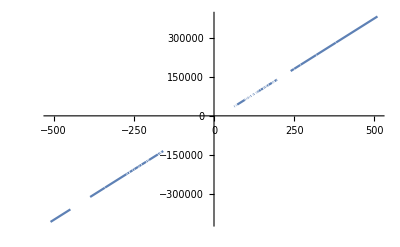

```mathematica
Plot[Ω, {t, -510, 510}]
```

```mathematica
Clear[r]
```

```mathematica
t = 503
```

503

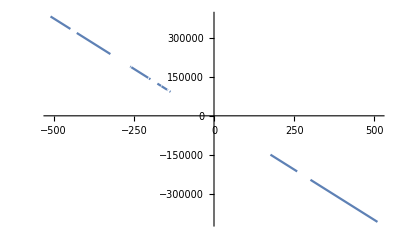

```mathematica
Plot[Ω, {r, -510, 510}]
```

# Δ dependence

```mathematica
Clear[t, Δ]
```

```mathematica
α = 503 - 503 I
```

503-503 ⅈ

```mathematica
FullSimplify[Ω]
```

-12800+(503 (127263527 (-67+2000000 √3)+300000 Δ (253009+150000000 Δ (5030 √3+3 Δ))))/(506250000000000 Δ^4)

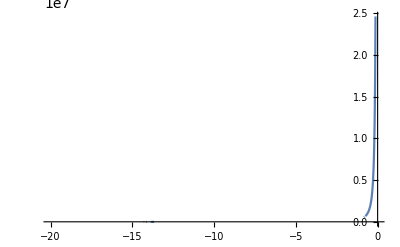

```mathematica
Plot[Ω, {Δ, -20, -10^-2}]
```

# n dependence

```mathematica
Clear[n]
```

```mathematica
Δ = -1
```

-1

```mathematica
α = 503 - 503 I
```

503-503 ⅈ

```mathematica
FullSimplify[Ω]
```

(113982077108162000000 √3-6547947467966223427 n)/506250000000000

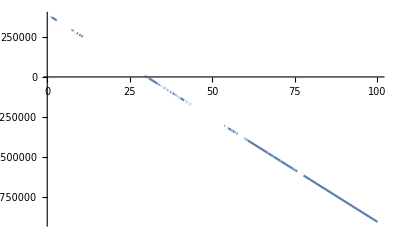

```mathematica
Plot[Ω, {n, 1, 100}]
```

# w dependence

```mathematica
Clear[w]
```

```mathematica
p = w/(2*κ)
```

w/2

```mathematica
n =1
```

1

```mathematica
FullSimplify[Ω]
```

(4 (-648/w+503 (45 (-3+5030 √3)-253009 w^2 (30-100600 √3+33701 w))))/2025

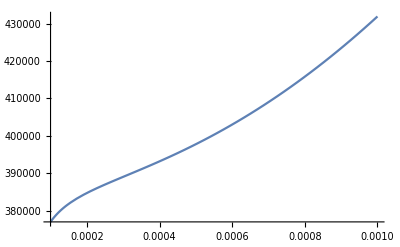

```mathematica
Plot[Ω, {w, 10^-4*κ, 10^-3*κ}]
```